```mathematica
Needs["DYNAMITE`"];
Needs["MaTeX`"];

texStyle={FontFamily->"Latin Modern Roman",FontSize->14};

style:={PlotStyle->Join[Lighter[Red,#]&/@Most[Subdivide[0.7,0.,10]],Darker[Red,#]&/@Most[Subdivide[0,0.7,10]]],Axes->False,AxesStyle->Directive[Black,FontSize->15,FontFamily->"Times"],Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameTicksStyle->{{Directive[FontFamily->"Times New Roman",FontSize->20,Black],Directive[FontOpacity->0,FontSize->0]},{Directive[FontFamily->"Times New Roman",FontSize->20,Black],Directive[FontOpacity->0,FontSize->0]}},ImageSize->Large,FrameStyle->Directive[Black,Thickness[.003]]};

styleInset:={PlotStyle->Join[Lighter[Red,#]&/@Most[Subdivide[0.7,0.,10]],Darker[Red,#]&/@Most[Subdivide[0,0.7,10]]],Axes->False,AxesStyle->Directive[Black,FontSize->12,FontFamily->"Times"],Frame->True,FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},FrameTicksStyle->{{Directive[FontFamily->"Times New Roman",FontSize->15,Black],Directive[FontOpacity->0,FontSize->0]},{Directive[FontFamily->"Times New Roman",FontSize->15,Black],Directive[FontOpacity->0,FontSize->0]}},ImageSize->Large,FrameStyle->Directive[Black,Thickness[.003]]};
```

```mathematica
(*data=ImportDMFE["/nobackups/jlang/Results_CPC/02_12_2025_2120_p=3_q=3_lambda=0.50_T0=inf_G=0.00_L=512/data.h5"];*)
data=ImportDMFE["/nobackups/jlang/Results_CPC/04_12_2025_0128_p=3_q=3_lambda=0.50_T0=inf_G=0.00_L=512/data.h5"];
```

```mathematica
energy2=Rest[Import["/nobackups/jlang/Results/21_09_2025_0009_p=3_q=3_lambda=0.30_T0=inf_G=0.00_L=512/energy.txt","Table"]][[All,-1]];
t1grid2=Rest[Import["/nobackups/jlang/Results/21_09_2025_0009_p=3_q=3_lambda=0.30_T0=inf_G=0.00_L=512/energy.txt","Table"]][[All,1]];
Etab2=Transpose[{t1grid2,energy2}];
```

```mathematica
rvec=data["Data","rvec"];
t1grid=data["Data","t1grid"];
energy=Rest[Import["/nobackups/jlang/Results_CPC/04_12_2025_0128_p=3_q=3_lambda=0.50_T0=inf_G=0.00_L=512/energy.txt","Table"]][[All,-1]];
Etab=Transpose[{t1grid,energy}];
```

```mathematica
bsearch=Compile[{{list,_Complex,1},{elem,_Real}},Block[{n0=1,n1=Length[list],m=0,diff1},While[n0<=n1,m=Quotient[n0+n1,2];
If[list[[m]]==elem,Return[m]];
If[list[[m]]<elem,n0=m+1,n1=m-1]];
diff1=Abs[list[[m]]-elem];
If[list[[m]]<elem,If[diff1<=Abs[list[[Min[m+1,Length[list]]]]-elem],m,m+1],If[diff1<=Abs[list[[Max[m-1,1]]]-elem],m,m-1]]],RuntimeAttributes->{Listable},CompilationTarget->"C"];
pos=DeleteDuplicates[bsearch[t1grid,2^Range[-10,21,.05]]];
Efunc[t_]=Interpolation[Developer`ToPackedArray[Etab[[pos]]],Method->"Spline",InterpolationOrder->5][t];
```

```mathematica
fλ[x_]:=x^3;
Eth:=Sqrt[Derivative[2][fλ][1]](fλ[1]/Derivative[2][fλ][1]-Derivative[1][fλ][1]/Derivative[2][fλ][1]-fλ[1]/Derivative[1][fλ][1]);
Block[{ind=100},FindFit[Transpose[{t1grid[[pos[[ind;;-1]]]],Log[Abs[(-t1grid[[pos[[ind;;-1]]]] Efunc'[t1grid[[pos[[ind;;-1]]]]])/(Efunc[t1grid[[pos[[ind;;-1]]]]]-Eth)-2/3]]}],{Log[Abs[α x^(-1/3)+β x^(-2/3)+γ x^-1]],-0.02<α<-0.01,0.3>β>.2,-.1>γ>-.2},{{α,-0.016},{β,0.25},{γ,-0.19}},x]]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

{α→-0.0159544,β→0.248921,γ→-0.188888}

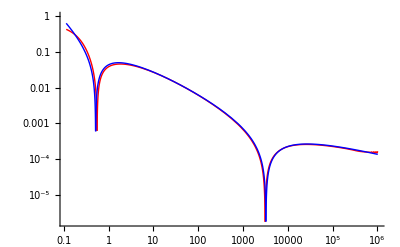

```mathematica
Block[{α=-0.0159544,β=0.248921,γ=-0.188888},LogLogPlot[{Abs[(-x Efunc'[x])/(Efunc[x]-Eth)-2/3],Abs[α x^(-1/3)+β x^(-2/3)+γ x^-1] },{x,t1grid[[pos[[100]]]],t1grid[[1350000]]},PlotStyle->{Directive[Red,Thick],Directive[Blue,Thick]}]]
```

```mathematica
FullSimplify[(-x D[Log[f[x]-e],x]-2/3)]
```

-2/3+(x f'[x])/(e-f[x])

```mathematica
MaTeX["\\frac{t E'(t)}{E(t)-E_\\text{th}}",Magnification->2.5]
```

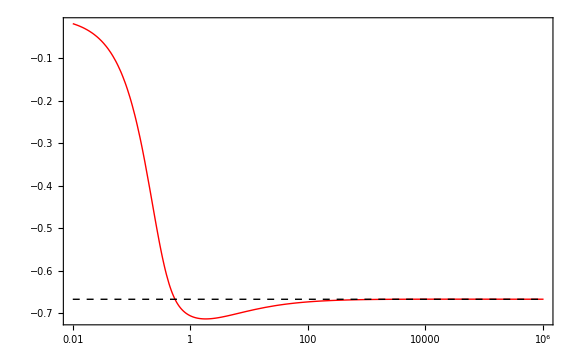

```mathematica
Block[{α=-0.0159544,β=0.248921,γ=-0.188888},LogLinearPlot[{(x Efunc'[x])/(Efunc[x]-Eth),-2/3 },{x,.01,t1grid[[1350000]]},PlotStyle->{Directive[Red,Thick],Directive[Black,Dashed,Thick]},PlotRange->Full,Evaluate[style],FrameLabel->{MaTeX["t",Magnification->2.5],MaTeX["t\\partial_t\\log(E(t)-E_\\text{th})",Magnification->2.5]},Epilog->Inset[LogLogPlot[{Abs[α x^(-1/3)+β x^(-2/3)+γ x^-1],Abs[(-x Efunc'[x])/(Efunc[x]-Eth)-2/3] },{x,t1grid[[pos[[100]]]],t1grid[[1350000]]},PlotStyle->{Directive[Black,Thick],Directive[Red,Thick]},Evaluate[styleInset],FrameLabel->{MaTeX["t",Magnification->1.5],MaTeX["|t\\partial_t\\log(E(t)-E_\\text{th})+2/3|",Magnification->1.5]}],{Log[600],-.33},Center,14.5]]]
```